Remove::rmnsm: There are no symbols matching ""Global`*"".

eigenState defined

1/1000000000

ρ0[r]

(3 ρ0[r])/(4 π)

ρ defined

eqn for m defined

condition for m defined

eqn for p defined

condition for p defined

ρ0=(3 ρ0[1/10000])/(4 π)

System defined

Rstar=3.47918×10^10km

Rmax=3.47918×10^10km

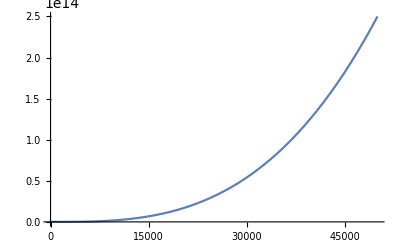

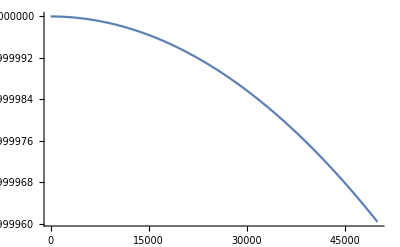

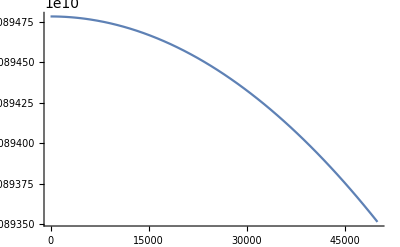

Radius=3.47918×10^10

Mass=7.7562×10^24

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
G:=6.67408*10^(-11)(*gravitational constant in SI units*)
c:=299792458(*speed of light in SI units*)
(*m[r]:=4/3 π r^3 ρ0*)
my0:=10^(-4);
κ:=0.3
RSun :=1;
MSun:=1;
rsSun:=2G*MSun/(c^2)
ρSun:=3 MSun/(4 π RSun^3);
Print["eigenState defined"];

d[my0]:=2;
(*K=c^2/(ρSun^(κ-1))*)
K=10^(-9)

d[r_]=ρ0[r]
ρ[r_]=ρSun d[r]
p[r_]=K*(G*ρSun /( c^2))^(κ-1)*(ρ[r])^(κ);
Print["ρ defined"];

eqnM:={m'[x]==3 x^2 d[x]}
Print["eqn for m defined"];
condM:={m[my0]==0}
Print["condition for m defined"]

eqnP:={-p'[x]==rsSun/(2 RSun x^2)((m[x]+3 x^3 p[x])(d[x]+p[x])/(1-m[x] rsSun/(x RSun)))}
Print["eqn for p defined"];
condP:={p[my0]==K/(ρSun * c^2)(ρSun d[my0])^κ}
Print["condition for p defined"];

condρ:={ρ[my0]==ρSun d[my0]}
Print["ρ0=",ρ[my0]];
stopCond:={WhenEvent[Evaluate[Re[ρ0[x]]<=0],rMax=x;"StopIntegration"]}
system:=Join[eqnM,eqnP,condM,condρ, stopCond];
Print["System defined"];
state=First[NDSolve`ProcessEquations[system, {m,ρ0}, {x, my0, ∞}]];
NDSolve`Iterate[state,∞]
sol=NDSolve`ProcessSolutions[state];
rStar=Last[state@"CurrentTime"[]];
Print["Rstar=",rStar,"km"];
Print["Rmax=",rMax,"km"];
(*rMax:=maxInt*)
(*sol=NDSolve[system, {p}, {r, my0, ∞}];*)
Plot[Evaluate[m[x]/.sol],{x,my0,50000*RSun},PlotRange->All]
Plot[Evaluate[ρ0[x]/.sol],{x,my0,50000*RSun},PlotRange->All]
Plot[Evaluate[p[x]/.sol],{x,my0,50000*RSun},PlotRange->All]
Print["Radius=",rMax,""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```